```mathematica
<<"/Users/raina/Documents/MathematicaNB/Dynamica1.m"
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

```mathematica
Clear[Ad,Bd,Ae,Be,qa,qb,td,tu,te,n,na,nrB,Zb,Z,Za]
ϵ=10^-5;
sysWExpCImiscomm=DynamicalSystem[{
Ae/te-Ad/(qa td),
Be/te-Bd/(qb td),
- Ae/te+(Ad/(td qa)+(1-Ad-Ae-Bd-Be)/tu)  (n (na)+(1-n)Ad/(Ad+Bd))+n na Bd/(td qb),
- Be/te+(Bd/(td qb)+(1-Ad-Ae-Bd-Be)/tu)  (n (1-na)+(1-n)Bd/(Ad+Bd))+n (1-na)Ad/(td qa)
},
{{Ad,-0.01,1+0.01},{Bd,-0.01,1+0.01},{Ae,-0.01,1+0.01},{Be,-0.01,1+0.01}},
{{tu,ϵ,5000},{te,0.01,5000},{td,1,5000},{qa,ϵ,1},{qb,ϵ,1},{n,0,1},{na,0,1}}]
```

DynamicalSystem[«4 ODEs»,{Ad,Bd,Ae,Be},{tu,te,td,qa,qb,n,na}]

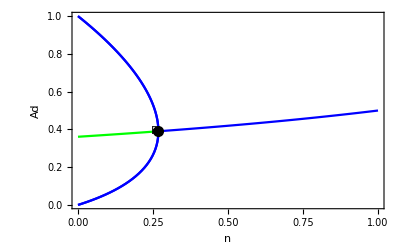

```mathematica
DisplayBifurcationDiagram[sysWExpCImiscomm/.{tu->1000,te->0.001,td->1300,qa->1,qb->1,na->0.5},n,StateVariables->{Ad},GridLines->{{},{}}]
```

```mathematica
ER = EquilibriumBranches[sysWExpCImiscomm/.{tu->1000,te->0.001,td->1300,qa->1,qb->0.82,na->0.5},n];
```

```mathematica
ER[[1]][[1]][[4]]
```

{{0.211821815857581,0.56868697727602,1.62939858351986×10^-7,5.33477464611651×10^-7,0.167018424567252},{0.21272268823835,0.567256747497051,1.63632837106423×10^-7,5.32135785644513×10^-7,0.167014604871297},{0.214526729525997,0.564397891916744,1.65020561173844×10^-7,5.29453932379685×10^-7,0.16698376282249},{0.218143124486079,0.558687265620715,1.6780240345083×10^-7,5.24096872064461×10^-7,0.166826535235707},{0.225401215542651,0.547300472621789,1.73385550417424×10^-7,5.13415077506369×10^-7,0.166106672560519},{0.239936458282482,0.524729162353923,1.8456650637114×10^-7,4.92241240482104×10^-7,0.162836925977994},{0.255055726869458,0.50140233341299,1.96196712976506×10^-7,4.70358661738265×10^-7,0.156234403765465},{0.269441159956084,0.47904962114346,2.07262430735449×10^-7,4.49389888502307×10^-7,0.145758617412284},{0.282418164406154,0.458320085796048,2.17244741850888×10^-7,4.29943795305862×10^-7,0.13098667609115},{0.293334277743906,0.439884690901535,2.25641752110697×10^-7,4.12649803847594×10^-7,0.112084263142201},{0.301880707933925,0.424090186943652,2.32215929179942×10^-7,3.97833196007178×10^-7,0.0898622311391744},{0.308192547345175,0.41081550838749,2.37071190265519×10^-7,3.85380401864437×10^-7,0.0653618204673257},{0.31265321662838,0.399658782491339,2.40502474329523×10^-7,3.74914430104445×10^-7,0.0394396981113895},{0.315677485409065,0.390171978363908,2.4282883493005×10^-7,3.66014989084342×10^-7,0.012659465169869},{0.31669618362872,0.386214858083805,2.43612448945169×10^-7,3.62302868746534×10^-7,0}}